```mathematica
a={a0,a1,a2};
b={b0,b1,b2};
c={c0,c1,c2};
X={x0,x1,x2};
Simplify[Dot[X-c,Inverse[{a-c,b-c,Cross[a-c,b-c]}]]-Dot[X-c,Inverse[{a-c,b-c,Cross[a-c,b-c]}]]]
```

{0,0,0}

```mathematica
d=Import["/Users/tomoaki/Desktop/static_pressure.csv"][[1]];
Column@Table[{i,d[[i]]},{i,1,Length[d]}]
```

Part::partw: {U:0,U:1,U:2,density,pressure,isSurface,isInsideOfBody,Points:0,Points:1,Points:2}の部分11は存在しません．

Part::partw: {U:0,U:1,U:2,density,pressure,isSurface,isInsideOfBody,Points:0,Points:1,Points:2}の部分12は存在しません．

Part::partw: {U:0,U:1,U:2,density,pressure,isSurface,isInsideOfBody,Points:0,Points:1,Points:2}の部分13は存在しません．

General::stop: この計算中に，Part::partwのこれ以上の出力は表示されません．

{1,U:0}
{2,U:1}
{3,U:2}
{4,density}
{5,pressure}
{6,isSurface}
{7,isInsideOfBody}
{8,Points:0}
{9,Points:1}
{10,Points:2}
{11,{U:0,U:1,U:2,density,pressure,isSurface,isInsideOfBody,Points:0,Points:1,Points:2}⟦11⟧}
{12,{U:0,U:1,U:2,density,pressure,isSurface,isInsideOfBody,Points:0,Points:1,Points:2}⟦12⟧}
{13,{U:0,U:1,U:2,density,pressure,isSurface,isInsideOfBody,Points:0,Points:1,Points:2}⟦13⟧}
{14,{U:0,U:1,U:2,density,pressure,isSurface,isInsideOfBody,Points:0,Points:1,Points:2}⟦14⟧}
{15,{U:0,U:1,U:2,density,pressure,isSurface,isInsideOfBody,Points:0,Points:1,Points:2}⟦15⟧}
{16,{U:0,U:1,U:2,density,pressure,isSurface,isInsideOfBody,Points:0,Points:1,Points:2}⟦16⟧}
{17,{U:0,U:1,U:2,density,pressure,isSurface,isInsideOfBody,Points:0,Points:1,Points:2}⟦17⟧}
{18,{U:0,U:1,U:2,density,pressure,isSurface,isInsideOfBody,Points:0,Points:1,Points:2}⟦18⟧}
{19,{U:0,U:1,U:2,density,pressure,isSurface,isInsideOfBody,Points:0,Points:1,Points:2}⟦19⟧}
{20,{U:0,U:1,U:2,density,pressure,isSurface,isInsideOfBody,Points:0,Points:1,Points:2}⟦20⟧}

```mathematica
all =10000;
n=10;
Sum[(n-i)/n*all,{i,0,n}]/Sum[all,{i,0,n}]
```

1/2

### 静水圧データ

```mathematica
ClearAll["Global`*"]
ρ=1000;
g=9.81;
s=0.1;

dataO=Import["/Users/tomoaki/Desktop/static_pressure.csv"];
dataT=Transpose[dataO];
ListPlot[
{Table[{h,ρ*g*(s-h)},{h,0,0.1,0.01}],
Transpose[{dataT[[14]],dataT[[5]]}]},
(*以下はオプション*)
Joined->{True,False},
Frame->True,
FrameStyle->Directive[Black],
FrameLabel->{"Depth [m]","Pressure [Pa]"},
LabelStyle->{FontFamily->"Times",FontSize->20},
FrameTicksStyle->Directive[Black, FontFamily->"Times",FontSize->20],
PlotRange->{{0,0.1},{-100,1100}},
GridLines->Automatic,
PlotStyle->{{Blue,Thick},{Red,Opacity->0.5}},
ImageSize->500
]
```

Part::partw: {{U:0,-0.014327,0.0088689,-6.4401×10^-8,0.0064415,0.000024869,-0.01702,-0.0057648,-0.012979,0.000081472,0.000026681,-0.0086958,-5.4895×10^-6,-0.014034,0.013684,-0.025751,0.00056507,-0.000056866,0.01601,-0.024961,0.021538,0.0065207,0.0040951,0.028826,-0.01235,-0.0064601,0.0080688,0.005613,-0.0061893,0.0053931,0.019539,-0.020796,0.014029,-0.0056121,0.010994,0.0089114,0.023675,-0.011283,-0.037871,0.0091655,0.027222,0.012619,-0.0024412,0.0064862,0.03223,-0.032,-0.023203,-0.024638,-0.006682,-0.025494,«3707»},«8»,{Points:2,0.072749,0.057988,0.094521,0.022881,0.088982,0.095791,0.083485,0.054618,0.096808,«31»,0.093181,0.081581,0.071333,0.055889,0.024511,0.10616,0.0094694,0.093249,0.075175,«3707»}}の部分14は存在しません．

Transpose::nmtx: {{{U:0,-0.014327,0.0088689,-6.4401×10^-8,0.0064415,0.000024869,-0.01702,-0.0057648,-0.012979,0.000081472,0.000026681,-0.0086958,-5.4895×10^-6,-0.014034,0.013684,-0.025751,0.00056507,-0.000056866,0.01601,-0.024961,0.021538,0.0065207,0.0040951,0.028826,-0.01235,-0.0064601,0.0080688,0.005613,-0.0061893,0.0053931,0.019539,-0.020796,0.014029,-0.0056121,0.010994,0.0089114,0.023675,-0.011283,-0.037871,0.0091655,0.027222,0.012619,-0.0024412,0.0064862,0.03223,-0.032,-0.023203,-0.024638,-0.006682,-0.025494,«3707»},«8»,{Points:2,0.072749,0.057988,0.094521,0.022881,0.088982,0.095791,0.083485,0.054618,0.096808,«32»,0.081581,0.071333,0.055889,0.024511,0.10616,0.0094694,0.093249,0.075175,«3707»}}⟦14⟧,{«1»}}の最初の2個のレベルは転置できません．

Part::partw: {{U:0,-0.014327,0.0088689,-6.4401×10^-8,0.0064415,0.000024869,-0.01702,-0.0057648,-0.012979,0.000081472,0.000026681,-0.0086958,-5.4895×10^-6,-0.014034,0.013684,-0.025751,0.00056507,-0.000056866,0.01601,-0.024961,0.021538,0.0065207,0.0040951,0.028826,-0.01235,-0.0064601,0.0080688,0.005613,-0.0061893,0.0053931,0.019539,-0.020796,0.014029,-0.0056121,0.010994,0.0089114,0.023675,-0.011283,-0.037871,0.0091655,0.027222,0.012619,-0.0024412,0.0064862,0.03223,-0.032,-0.023203,-0.024638,-0.006682,-0.025494,«3707»},«8»,{Points:2,0.072749,0.057988,0.094521,0.022881,0.088982,0.095791,0.083485,0.054618,0.096808,«31»,0.093181,0.081581,0.071333,0.055889,0.024511,0.10616,0.0094694,0.093249,0.075175,«3707»}}の部分14は存在しません．

Transpose::nmtx: {{{U:0,-0.014327,0.0088689,-6.4401×10^-8,0.0064415,0.000024869,-0.01702,-0.0057648,-0.012979,0.000081472,0.000026681,-0.0086958,-5.4895×10^-6,-0.014034,0.013684,-0.025751,0.00056507,-0.000056866,0.01601,-0.024961,0.021538,0.0065207,0.0040951,0.028826,-0.01235,-0.0064601,0.0080688,0.005613,-0.0061893,0.0053931,0.019539,-0.020796,0.014029,-0.0056121,0.010994,0.0089114,0.023675,-0.011283,-0.037871,0.0091655,0.027222,0.012619,-0.0024412,0.0064862,0.03223,-0.032,-0.023203,-0.024638,-0.006682,-0.025494,«3707»},«8»,{Points:2,0.072749,0.057988,0.094521,0.022881,0.088982,0.095791,0.083485,0.054618,0.096808,«32»,0.081581,0.071333,0.055889,0.024511,0.10616,0.0094694,0.093249,0.075175,«3707»}}⟦14⟧,{«1»}}の最初の2個のレベルは転置できません．

Part::partw: {{U:0,-0.014327,0.0088689,-6.4401×10^-8,0.0064415,0.000024869,-0.01702,-0.0057648,-0.012979,0.000081472,0.000026681,-0.0086958,-5.4895×10^-6,-0.014034,0.013684,-0.025751,0.00056507,-0.000056866,0.01601,-0.024961,0.021538,0.0065207,0.0040951,0.028826,-0.01235,-0.0064601,0.0080688,0.005613,-0.0061893,0.0053931,0.019539,-0.020796,0.014029,-0.0056121,0.010994,0.0089114,0.023675,-0.011283,-0.037871,0.0091655,0.027222,0.012619,-0.0024412,0.0064862,0.03223,-0.032,-0.023203,-0.024638,-0.006682,-0.025494,«3707»},«8»,{Points:2,0.072749,0.057988,0.094521,0.022881,0.088982,0.095791,0.083485,0.054618,0.096808,«31»,0.093181,0.081581,0.071333,0.055889,0.024511,0.10616,0.0094694,0.093249,0.075175,«3707»}}の部分14は存在しません．

General::stop: この計算中に，Part::partwのこれ以上の出力は表示されません．

Transpose::nmtx: {{{U:0,-0.014327,0.0088689,-6.4401×10^-8,0.0064415,0.000024869,-0.01702,-0.0057648,-0.012979,0.000081472,0.000026681,-0.0086958,-5.4895×10^-6,-0.014034,0.013684,-0.025751,0.00056507,-0.000056866,0.01601,-0.024961,0.021538,0.0065207,0.0040951,0.028826,-0.01235,-0.0064601,0.0080688,0.005613,-0.0061893,0.0053931,0.019539,-0.020796,0.014029,-0.0056121,0.010994,0.0089114,0.023675,-0.011283,-0.037871,0.0091655,0.027222,0.012619,-0.0024412,0.0064862,0.03223,-0.032,-0.023203,-0.024638,-0.006682,-0.025494,«3707»},«8»,{Points:2,0.072749,0.057988,0.094521,0.022881,0.088982,0.095791,0.083485,0.054618,0.096808,«32»,0.081581,0.071333,0.055889,0.024511,0.10616,0.0094694,0.093249,0.075175,«3707»}}⟦14⟧,{«1»}}の最初の2個のレベルは転置できません．

General::stop: この計算中に，Transpose::nmtxのこれ以上の出力は表示されません．

ListPlot::lpn: {{{0.,981.},{0.01,882.9},{0.02,784.8},{0.03,686.7},{0.04,588.6},{0.05,490.5},{0.06,392.4},{0.07,294.3},{0.08,196.2},{0.09,98.1},{0.1,0.}},{}}は数値のリストあるいは数値の対のリストではありません．

General::stop: この計算中に，ListPlot::lpnのこれ以上の出力は表示されません．

ListPlot[1]
 |  |  |  |

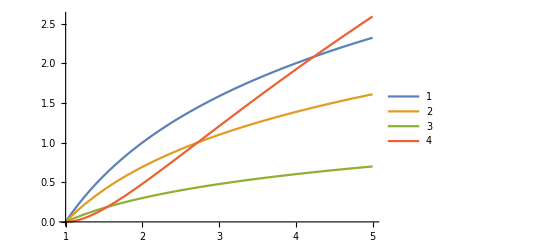

```mathematica
Plot[{Log2[x],Log[x],Log10[x],Log[x]^2},{x,1,5},PlotLegends->Automatic]
```